## 类神经网路的原理介绍 以及其在 Wolfram 语言里的使用

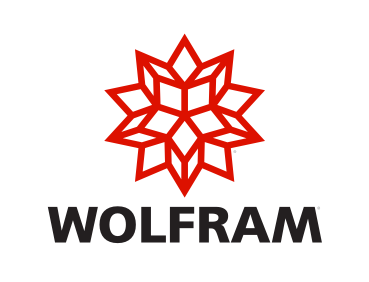
## 

© Wolfram Research, Inc.

## What are Neural Networks?

## 什么是神经网络？

As usual in Machine learning, the goal of neural network is to determine an appropriate model for given prediction task. - 与机器学习算法一样，神经网络的目标是为给预测任务确定一个合适的模型.

The neural network’s structure is biologically inspired by our nervous system. - 神经网络的结构是受到我们生物学上的神经系统的启发.

Its structure consists of “neurons” organized in “layers” through which information is processed from the input to the output tensor. - 它的结构由组织成“层”的“神经元”组成，通过这些“神经元”，输入信息经过处理传送到输出张量.

```mathematica
Source:http://cs231n.github.io/neural-networks-1/
```

For given input data (images, text,...) the output provides a task-oriented prediction once the network has been “trained”. -  对于给定的输入数据（图像、文本等），一旦对网络进行“训练”，输出将提供任务导向的预测.

The layers may contain learnable parameters - 这些层架构里可能包含可學習参数.

During training, the optimization minimizes the mismatch between predicted and actual output for given training data. - 在训练网络期间，对于给定的训练数据，优化参数可以逐渐地减少预测输出与实际输出之间的不匹配.

The model inside the neural network eventually forms after training for prediction task. - 在完成针对预测任务的训练后，神经网络内部的模型最终形成.

## The main aspects of Neural Networks

## 神经网络的主要观点

### The components or layers:

### 组件或层：

Neural Networks are constructed from different operational layers.- 神经网络由不同的”作用”层构成.

Each layer operates on its input, and passes its output as input to the next layer. - 每一层都在其输入上进行操作，并将其输出传递到下一网络层作为输入.

A layer may: - ”作用”层可以：

introduce nonlinearity through activation functions - 通过激活函数引入非线性

have learnable parameters, e.g. ConvolutionLayer, linear layer - 具有可学习的参数，例如 卷积层、线性层

introduce regularization, e.g.  batch normalization layer - 引入正则化，例如：（批）规范化层

introduce randomness, e.g.   dropout layer - 引入随机性，例如： dropout层

### The architectures and models:

### 架构和模型：

Are highly task-oriented. - 高度任务导向.

Their varieties include the choices of layers, their sequence and topology. - 架构和模型的变化取决于层的选择、序列和拓扑.

NetChain and NetGraph allow building any architecture from scratch. - NetChain 和 NetGraph 允许从头开始构建任何体系结构.

Alternatively, many useful ones (LeNet,  GoogleNet, VGG, ResNet, ...) can be imported from the Wolfram Neural Net Repository. - 或者，可以从 Wolfram 神经网络存储库导入许多有用的 LeNet、GoogleNet、VGG、ResNet等

### Optimization and the loss function (for training):

### （用于训练的）优化和损失函数：

The parameters of built neural network need to be updated to learn an appropriate model for a given task and data. - 需要优化神经网络的参数，以学习针对给定任务和数据的适当模型.

The loss function quantifies the mismatch between the current model prediction and its target output for a given input. - 损失函数可量化当前模型给出的预测与其既定目标之间的差距.

The (task-oriented) loss function guides a neural network to learn useful information from data. - （任务导向的）损失函数指导神经网络从数据中学习有用的信息.

During “training the (neural) network”, the model’s parameters get optimized to minimize the loss function. - 在“训练（神经）网络”期间，优化模型的参数以最小化损失函数.

Gradient Descent Methods are typically used to update the parameters. In each step: w_(n+1)=w_n-lr  ∇L[w] 
Here w is the learnable parameters, L[w] is the loss function, and lr is learning rate which control the step size. 
- 梯度下降法通常用于更新参数. 在每个步骤中： w_(n+1)=w_n-lr  ∇L[w] . 其中，w 是学习参数，L [w]是损失函数，而 lr 是控制每次更新强度的学习率.

```mathematica
-Graphics-                 -Graphics-
```

Source: http://sebastianraschka.com/faq/docs/closed-form-vs-gd.html

#### All the components, the architecture, and the optimization work together to determine the model. - 包括组件的选取、网络架构,和优化方法 都对模型的确定有所贡献.

## Learning Objectives

## 学习目标

### Input Data

### 输入数据

Neural networks internally transfer information as numeric tensors. So first we need to understand how to convert different data types to tensors.

神经网络在内部将信息以数值张量的形式传递. 因此，首先我们需要了解如何将不同的数据类型转换为张量.

Encoders (and Decoders) - 编码（和解码）

### Network Structure

### 网络结构

Complicated neural networks are built up from a few foundational layer types. To understand more advanced networks, we must first familiarize ourselves with the basic constructs, including

复杂的神经网络是由一些基础类型的作用层构成的. 要了解更高级的网络，我们必须首先熟悉基本结构，包括：

Activation functions and ElementwiseLayer - 激活函数和 ElementwiseLayer

Other basic layers such as LinearLayer, ConvolutionLayer, PoolingLayer, BatchNormalizationLayer, DropoutLayer - 其他基本层，例如： LinearLayer、ConvolutionLayer、PoolingLayer、BatchNormalizationLayer、DropoutLaye

Network Constructors: NetChain and NetGraph - 网络构造函数：NetChain 和 NetGraph

### Network Training

### 网络训练

Given a neural network, the function NetTrain can train these networks in an optimized fashion:

给定一个神经网络，函数 NetTrain 可以优化的方式训练这些网络：

Training theory review and NetTrain - 訓練理论以及 NetTrain

Basic examples - 基本范例

Options: LossFunction, BatchSize, Method, TargetDevice, MaxTrainingRounds - 选项：LossFunction, BatchSize, Method, TargetDevice, MaxTrainingRounds

### Examples

### 例子

Basic Regression - 基本回归

Regression on RealWorld Data - 数据的回归

## Class Encoder : Class to Integer (Scalar)

## 类编码器：类->整数（标量）

NetEncoder is used to convert any data we receive to an input tensor. Similarly, after we have done the optimization (training), we convert the output tensor to the data format we started with using NetDecoder.

NetEncoder 用于将我们收到的任何数据转换为输入张量. 同样，在完成优化（训练）之后，我们将输出张量转换为使用NetDecoder 的数据格式.

#### Class encoders (class to scalar): 类别编码器（类->标量）：

Encode the user defined class (here the class of male and females)

用于编码用户定义的类（这里是男性和女性的类）

```mathematica
enc=NetEncoder[{"Class",{"male","female"}}]
```

NetEncoder[<>]

Use it to create the input tensor

用它来创建神经网络输入的张量：

```mathematica
enc[{"male","female","female"}]
```

{1,2,2}

#### Class decoders (vector to class): 类别解码器（向量->类别）：

Create the decoder for the same classes

为相同的类别们创建解码器：

```mathematica
dec=NetDecoder[{"Class",{"male","female"}}]
```

NetDecoder[<>]

Use a probabilistic approach (two weights for two classes) to decode the 2-D vector input.

使用概率方法（两个类具有两个权重）来解码输入的二维向量.

```mathematica
dec[{{1,2},{0.9,0.7}}]
```

{female,male}

```mathematica
Clear["Global`*"]
```

## Text Encoder : Text to Tensor (Rank 1)

## 文本编码器：文本->张量（1 阶）

#### Text Decoders (text to tensor): 文本编码器（文本->张量）：

We treat the class label as text input using a text encoder

我们使用文本编码器将类标签视为文本输入：

```mathematica
enc=NetEncoder[{"Characters",{"male","female"}}]
enc[{"male","female","female"}]
```

NetEncoder[<>]

{{1,2,3,4},{5,4,1,2,3,4},{5,4,1,2,3,4}}

#### Text Decoders (tensor to text): 文本解码器（张量 ->文本）：

```mathematica
dec=NetDecoder[{"Characters",{"a","b","c"}}]
dec[{{1,0,0},{1,0,0},{0,0,1},{0,1,0}}]
```

NetDecoder[<>]

aacb

```mathematica
Clear["Global`*"]
```

## Image Encoder : Image to Tensor (Rank 2 or 3)

## 图像编码器：图像->张量（2 阶或 3 阶）

#### Encode an image: 编码图像：

Make an Image encoder (3x128x128 is the default size of the output tensor)

制作图像编码器（3x128x128是输出张量的默认大小）：

```mathematica
enc=NetEncoder["Image"]
```

NetEncoder[<>]

Generate an image

产生图像：

```mathematica
im =Image[({{0.1, 0.2, 0.3}, {0.4, 0.5, 0.6}, {0.7, 0.7, 0.9}})]
```

-Graphics-

Encode the image

编码图像：

```mathematica
enc[im]
```

{{1},{1},{{0.1,0.1,124,0.3,0.3},{1},125,{1}}}
 |  |  |  |

Check the output dimensions

检查输出尺寸：

```mathematica
%//Dimensions
```

{3,128,128}

#### Decode to an image: 解码为图像：

Define an image decoder

定义图像解码器：

```mathematica
dec=NetDecoder[{"Image"}]
```

NetDecoder[<>]

Create a 3x3x3 tensor

创建一个 3x3x3 张量：

```mathematica
re={1,0,0};bl={0,0,1};gr={0,1,0};data=Transpose[{{re,bl,bl},{re,gr,bl},{re,re,bl}},{2,3,1}];
```

Decode the tensor to an image

将张量解码为图像：

```mathematica
dec[data]
```

-Graphics-

```mathematica
Clear["Global`*"]
```

## Audio Encoder : Audio to Tensor (Sequence)

## 音频编码器：音频->张量（序列）

Get an audio sample from ExampleData

从 ExampleData 获取音频样本：

```mathematica
a = ExampleData[{"Audio","Cat"}]
```

Make an Audio encoder

制作音频编码器：

```mathematica
enc=NetEncoder[{"Audio","Normalization"->{"Max",.5}}]
```

NetEncoder[<>]

Encode the audio and check the output dimension

编码音频并检查输出尺寸：

```mathematica
encOut = enc[a]; 
encOut//Dimensions
```

{15167,1}

Plot the encoded result

绘制编码结果：

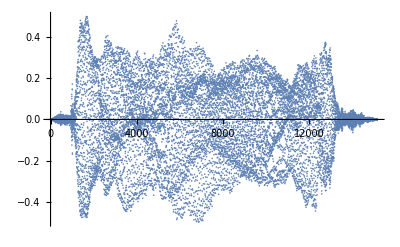

```mathematica
ListPlot[encOut //Flatten]
```

```mathematica
Clear["Global`*"]
```

## Network Structure -网络结构

## Activation functions and ElementwiseLayer I

## 激活函数和 ElementwiseLayer I

### Activation function (AF)

### 激活函数（AF）

AF determines if a neuron can be fired or not. - AF 确定是否可以激活神经元.

AF introduces non-linearity to increase the representational power of the network.- AF 引入了非线性，以增加网络的表达能力.

AF is a key component for neural networks - AF是神经网络的关键组件.

### ElementwiseLayer

ElementwiseLayer[f] : represents a net layer that applies an AF to every element of the input array. - 表示能将 AF 应用于输入数组的每个元素的网络层.

ElementwiseLayer[“name”]: applies the AF specified by “name”  listed below. - 经由选定下面列出的 “name” 来应用 AF.

|  | "RectifiedLinearUnit" or "ReLU" | Ramppaclet:ref/Ramp[x]
       |  | "ExponentialLinearUnit" or "ELU" | x when x≥0
Exppaclet:ref/Exp[x]-1 when x<0
       |  | "ScaledExponentialLinearUnit" or "SELU" | 1.0507 x when x >= 0
1.7581 (Exppaclet:ref/Exp[x]-1) when x<0
       |  | "SoftSign" | x/(1+Abspaclet:ref/Abs[x])
       |  | "SoftPlus" | Logpaclet:ref/Log[Exppaclet:ref/Exp[x+1]]
       |  | "HardTanh" | Clippaclet:ref/Clip[x,{-1,1}]
       |  | "HardSigmoid" | Clippaclet:ref/Clip[(x+1)/2, {0,1}]
       |  | "Sigmoid" | LogisticSigmoidpaclet:ref/LogisticSigmoid[x]

## Activation Function and ElementwiseLayer II

## 激活函数和 ElementwiseLayer II

Construct the ReLU function

构造 ReLU 函数：

```mathematica
MyReLU =If[#<0,0,#]&;
```

Apply ReLU by function MyReLU

通过函数 MyReLU 执行 ReLU：

```mathematica
ElementwiseLayer[MyReLU]  
%[{{1,2,3},{-1,-2,-3}}]
```

ElementwiseLayer[<>]

{{1.,2.,3.},{0.,0.,0.}}

Use the built-in “ReLU”

使用内置的 “ ReLU”：

```mathematica
ElementwiseLayer["ReLU"] 
%[{{1,2,3},{-1,-2,-3}}]
```

ElementwiseLayer[<>]

{{1.,2.,3.},{0.,0.,0.}}

## LinearLayer

### Principle

### 原则

目的: 利用权重 w跟偏差b 对输入做重整后更有效地成为下一层输入

LinearLayer[n] represents a trainable, fully connected layer that computes w.x+b with weights w, bias b, and of output dimension n. 
- LinearLayer[n] 表示可训练的完全连接的网络层，该网络层使用权重 w，偏差 b 和输出尺寸 n 计算输出 w.x+b.

### Basic usage in Wolfram Language

### Wolfram 语言的基本用法

Create a randomly initialized LinearLayer with input dimension 3 and output dimension 5 :

创建输入维度为 3 和输出维度为 5 的随机初始化的 LinearLayer：

```mathematica
linear=NetInitialize@LinearLayer[5,"Input"->3]
```

LinearLayer[<>]

Use a specific weight matrix and bias vector:

使用特定的权重矩阵和偏差向量：

```mathematica
w={{20,20},{-20,-20}};
b={-10,+30};
linear=LinearLayer[2,"Input"->2,"Weights"->w,"Biases"->b]
```

LinearLayer[<>]

Compare the result with the equivalent matrix operation:

将结果与等效矩阵运算进行比较：

```mathematica
{linear[{1,1}],w.{1,1}+b}
```

{{30.,-10.},{30,-10}}

```mathematica
Clear["Global`*"]
```

## ConvolutionLayer - 卷积网络层

### Principle

### 原则

目的: 利用滤波做卷积以提取有效的讯息

What is convolution  - 什麼是卷积: -Graphics-     for the one element of output - 对于输出里的一个元素 :  0x0+1x1+3x2+4x3 =19
					https://d2l.ai/chapter_convolutional-neural-networks/conv-layer.html

ConvolutionLayer[n,s] represents a trainable convolutional net layer with n output channels( i.e. n filters for each input channel), and using kernels of size s to compute the convolution.
- 表示具有 n 个输出通道（即每个输入通道對應 n 个滤波）的可训练卷积网络层，并使用大小为 s 的内核来计算卷积.

For  2D image convolution, you can create a 2d convolution layer with kernel size of h * w as: ConvolutionLayer[n,{h,w}]
- 对于 2D 图像卷积，用来创建内核大小为 h * w 的 2d 卷积层为：ConvolutionLayer [n，{h，w}]

### Basic usage in Wolfram Language

### 在Wolfram 语言里的基本用法

Specify a convolution layer with 2 output channels, filter size 2x2, and input shape {1,4,4}

指定具有 2 个输出通道，滤波器大小为 2x2 和输入形状为 {1,4,4} 的卷积层：

```mathematica
conv=NetInitialize@ConvolutionLayer[2,{2,2},"Input"->{1,4,4}]
```

ConvolutionLayer[<>]

Generate a random input

产生随机输入：

```mathematica
sample=RandomReal[1,{1,4,4}];
```

Convolute each channel separately:

分别对每个通道进行卷积：

```mathematica
MatrixForm/@conv[sample]
```

{(0.59985 | 0.663414 | 0.265291
0.489189 | 0.572853 | 0.540685
0.734866 | 0.596651 | 0.382534),(0.0975606 | -0.13711 | 0.0119504
0.319117 | 0.0693607 | 0.0574651
0.0755305 | -0.0250186 | -0.0418367)}

Extract the weights (both channels have filters of size 2x2):

提取权重（两个通道的滤波器大小均为 2x2）：

```mathematica
NetExtract[conv,"Weights"]//Normal//MatrixForm
```

((-0.197071 | 0.292753
0.366997 | 0.332751)
(0.205897 | -0.0593746
-0.383721 | 0.321939))

### Strides 步长

“Stride” defines how many pixels the filter moves to generate the next convolution output pixel.
- “Stride” 定义滤波器移动多少像素以生成下一个卷积输出像素。

The following shows the examples of stride 1 (left) and stride 2 (right) for input {0,1,2,-1,1,-3,0}  with filter {1,0,-1}, - 下面显示了使用滤波 {1,0，-1} 以及输入 {0,1,2，-1,1，-3,0} 的 步长 1（左）和 步长 2（右）示例，

					stride 1                                                         	 	stride 2                 				     	 filter

-Graphics-

http://cs231n.github.io/convolutional-networks/

ConvolutionLayer by default uses stride 1: - 默认情况下，ConvolutionLayer 使用 步长 1：

```mathematica
list = {{0,1,2,-1,1,-3,0}};
```

```mathematica
conv=ConvolutionLayer["Weights"->{{{1,0,-1}}},"Biases"->None];
conv[list]
```

{{-2.,2.,1.,2.,1.}}

With stride 2: - 步长 2：

```mathematica
conv=ConvolutionLayer["Weights"->{{{1,0,-1}}},"Biases"->None,"Stride"->2];
conv[list]
```

{{-2.,1.,1.}}

Another animation of convolution with strides. - 带有 Stride 的其他卷积动画.

### Padding

### 填白

Padding refers to the amount of zero-valued pixels added to the edges of an input image when it is being processed by the kernel of a CNN - 填白是指当 CNN 的内核对其进行处理时，添加到输入图像边缘的零值像素的数量.

Padding with 0s of padding-size 1 (input in light blue, output in green, and filter in yellow):

填白大小为 1 的填充为 0（浅蓝色输入，绿色输出，黄色滤波器）：

From https://www.pyimagesearch.com/2018/12/31/keras-conv2d-and-convolutional-layers/

Calculating it in Wolfram Language:

用 Wolfram 语言进行计算：

Setup the input and filter. - 设置输入和滤波.

```mathematica
input = {{{60,113,56,139,85},{73,121,54,84,128},{131,99,70,129,127},{80,57,115,69,134},{104,126,123,95,130}}};
filter = {{{{0,-1,0},{-1,5,-1},{0,-1,0}}}};
```

Padding with 0s of size 1 on every side. - 在每边填白.

```mathematica
inputPad = ArrayPad[input[[1]],1];
MatrixForm/@{input[[1]],inputPad}
```

{(60 | 113 | 56 | 139 | 85
73 | 121 | 54 | 84 | 128
131 | 99 | 70 | 129 | 127
80 | 57 | 115 | 69 | 134
104 | 126 | 123 | 95 | 130),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 60 | 113 | 56 | 139 | 85 | 0
0 | 73 | 121 | 54 | 84 | 128 | 0
0 | 131 | 99 | 70 | 129 | 127 | 0
0 | 80 | 57 | 115 | 69 | 134 | 0
0 | 104 | 126 | 123 | 95 | 130 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

Build two convolution layers of the same filter but with padding sizes 1 and 0 respectively. 
- 构建相同滤波的两个卷积层，但填白大小分别为 1 和 0.

```mathematica
convPad1=ConvolutionLayer[1,{3,3},"Input"->{1,5,5},"Weights"->filter,"Biases"->{0.} ,"PaddingSize"->1,"Stride"->1]
convPad0=ConvolutionLayer[1,{3,3},"Input"->{1,7,7},"Weights"->filter,"Biases"->{0.} ,"PaddingSize"->0,"Stride"->1]
```

ConvolutionLayer[<>]

ConvolutionLayer[<>]

Input with a padding-size 1 convolution layer is equivalent to padded input with a padding-size 0 convolution layer:  
- 填白大小为 1 的卷积层作用在输入将等效于填白大小为 0 的卷积层作用在预先填白的输入：

```mathematica
MatrixForm/@{
Transpose[convPad1[input],2<->3],
Transpose[convPad0[{inputPad}],2<->3]
}
```

{((114.
53.
403.
108.
314.) | (328.
266.
116.
-135.
346.) | (-26.
-61.
-47.
256.
279.) | (470.
-30.
295.
-128.
153.) | (158.
344.
244.
344.
421.)),((114.
53.
403.
108.
314.) | (328.
266.
116.
-135.
346.) | (-26.
-61.
-47.
256.
279.) | (470.
-30.
295.
-128.
153.) | (158.
344.
244.
344.
421.))}

```mathematica
Clear["Global`*"]
```

## PoolingLayer 池化

### Principle

### 原则

目的: 减小输入在空間維度的大小

Pooling downsamples an input tensor with specific feature selection within each sub-region binned, thereby reduces input sizes. -藉由对每个分装的子区域内进行特定特征选择以达成对输入张量的池化下采样，从而减小输入的大小.

The feature selection within each window, i.e. the downsampling function, can be various functions like Max, Mean, Total, or others. - 在每個子区域内進行特征选择，即下采样函数，可以是各种函数，例如 Max、Mean、Total 或其他。

PoolingLayer[kernel, stride] represents a layer that uses stride as the step size between kernel applications.
- PoolingLayer [kernel，stride] 表示一个使用 stride 作为内核应用之间步长的层.

Picking a specific {1,4,4} tensor:

选择一个特定的 {1,4,4} 张量：

```mathematica
matrix = {{{12,7,0,86},{19,8,0,12},{27,5,23,4},{97,12,35,60}}};
matrix[[1]]//MatrixForm
```

(12 | 7 | 0 | 86
19 | 8 | 0 | 12
27 | 5 | 23 | 4
97 | 12 | 35 | 60)

### Max pooling layer of size 2x2 with stride 2

### 步长(Stride)为 2 的 2x2 大小的极大选取池化层

-Graphics-

Picking the maximum value from a given pool.

从给定的池中选择最大值.

Creating the pooling layer:

创建池层：

```mathematica
plMax = PoolingLayer[2,2,"Function"->Max]
```

PoolingLayer[<>]

Applying the layer:

应用該池化层：

```mathematica
MatrixForm/@plMax[matrix]
```

{(19. | 86.
97. | 60.)}

### Mean pooling layer of size 2x2 with stride 2

### 步长 Stride 为 2 的 2x2 大小的均值选取池化层

-Graphics-

Computing the average of each pool.

计算每个池的平均值.

Creating the pooling layer:

创建池层：

```mathematica
plMean = PoolingLayer[{2,2},2,"Function"->Mean]
```

PoolingLayer[<>]

Applying the layer:

应用該池化层：

```mathematica
MatrixForm/@plMean[matrix]
```

{(11.5 | 24.5
35.25 | 30.5)}

```mathematica
Clear["Global`*"]
```

#### Reference

https://principlesofdeeplearning.com/index.php/2018/08/27/is-pooling-dead-in-convolutional-networks/

## BatchNormalizationLayer - 批量归一化

### Principle

### 原则

目的: 减少”不稳定性”问题，提高”学习”效率.

### Basic normalization in statistics

### 统计的基本归一化

In a dataset, all the features (columns) may not be in same range, e.g. Price of house (in thousands of dollars) vs Age of house (in 0-100 years).  - 在数据集中，所有要素（列）可能不在同一范围内，例如：房屋价格（千美元）与房屋年龄（0至100年）.

Normalization to standard score is to convert the distribution of all inputs to have mean=0 and standard deviation=1.
- 归一化为标准分数是将所有输入的分布转换为均值= 0 和标准差= 1.

-Graphics-

https://medium.com/@ilango100/batch-normalization-speed-up-neural-network-training-245e39a62f85

### Batch Normalization (BN)

### 批量归一化,批规范化（BN）

Using Batch Normalization on input of each layer is helpful to reduce the “instability” issue and make “learning” more efficient. - 对各层输入进行批量归一化，有助于减少“不稳定性”问题，提高“学习”效率.

For a given activation layer Y=F(Z), where Z is output from previous layer, the new formula becomes Y=F(BN(Z)). - 对于给定的激发层 Y=F(Z)，其中 Z 是前一层的输出，新的公式为 Y=F(BN(Z)).

Normalization is done over ‘mini-batches’, for each channel. Hence the name ‘batch’ normalization. - 给定每个”小批量”样本,分别对每个通道进行归一化处理. 因此得名”批”归一化.

Training algorithm, for each channel: - 每个通道的训练算法：

-Graphics-       
		copied from the Paper by Ioffe and Szegedy

where: - 其中：

mean μ and variance σ.b2 of the mini-batch are evaluated for each channel - 对每个通道小批量的均值 μ 和方差 σ.b2 进行计算

normalize every batch input by subtracting mean μ and dividing it by standard deviation σ. (The epsilon ε is to prevent denominator from being zero) - 通过减去平均值 μ，然后除以标准差 σ 来归一化化每批输入. (epsilon ε 是为了防止分母为零.)

learnable parameters γ and β help scaling and shifting for getting better normalization. - 可学习参数 γ 和β 帮助缩放和平移得到更好的归一化.

The inference time requires the “population average” of the means and variances from the training. Practically, the moving mean and moving variance with a “momentum” α  are used. - 测试时需要训练期间的平均值和方差的”总体平均”. 但实际操作上，更倾向使用带有”动量” α 的移动平均和移动方差.

-Graphics-

### Batch Normalization in Wolfram Language

### Wolfram 语言中的批量归一化

BatchNormalizationLayer[] represents a trainable net layer that normalizes its input data by learning the data mean and variance. - 表示一个可训练的网络层，该网络层通过学习数据的平均值和方差对输入数据进行归一化.

Create an initialized BatchNormalizationLayer that takes a vector and returns a vector:

创建一个初始化的 BatchNormalizationLayer，它接受一个向量并返回一个向量：

```mathematica
batch=NetInitialize@BatchNormalizationLayer["Input"->2]
```

BatchNormalizationLayer[<>]

Apply the layer to an input vector:

将层应用于输入向量：

```mathematica
input = {{1,0},{-1,1}};
batch[input]
```

{{0.9995,0.},{-0.9995,0.9995}}

Normalize the input with σ=1 and ε=0.001 for reconstructing the evaluation.

利用 σ= 1 和 ε= 0.001模拟归一化计算.

```mathematica
input/(1+0.001)^.5
```

{{0.9995,0.},{-0.9995,0.9995}}

Extract and check the “Biases“, “MovingMean “, “MovingVariance”, “Scaling“ parameters:

提取并检查“偏差”、“移动平均值”、“移动变量”、“缩放”参数：

```mathematica
Normal/@Information[batch,"Arrays"]
```

<|{Biases}→{0.,0.},{MovingMean}→{0.,0.},{MovingVariance}→{1.,1.},{Scaling}→{1.,1.}|>

Use NetEvaluationMode to set the BatchNormalizationLayer to Training mode instead of default Testing mode:

使用 NetEvaluationMode 将 BatchNormalizationLayer 设置为训练模式，而不是默认的测试模式：

```mathematica
batch[input,NetEvaluationMode->"Train"]
```

{{0.9995,-0.998006},{-0.9995,0.998006}}

BatchNormalizationLayer is commonly inserted between a ConvolutionLayer and its activation function in order to stabilize and speed up training:

通常将 BatchNormalizationLayer 插入 ConvolutionLayer 及其激励函数之间，以稳定并加速训练：

```mathematica
NetChain[{ConvolutionLayer[3,{3,3}],BatchNormalizationLayer["Input"->{3,28,28}],ElementwiseLayer[Ramp]}]
```

NetChain[<>]

Setting the parameters explicitly:

设置参数：

```mathematica
layer=BatchNormalizationLayer["Scaling"->{3},"Biases"->{2},"MovingMean"->{1},"MovingVariance"->{2},"Epsilon"->0.001]
```

BatchNormalizationLayer[<>]

Double-check:

确认参数：

```mathematica
Normal/@Information[layer,"Arrays"]
```

<|{Biases}→{2.},{MovingMean}→{1.},{MovingVariance}→{2.},{Scaling}→{3.}|>

```mathematica
Clear["Global`*"]
```

## DropoutLayer

### Principle

### 原理

目的: 防止神经网络过度拟合- Prevent Neural Networks from Overfitting

Training Phase: - 训练阶段:

ignore (set to zero) a random fraction p of neurons in the layer - 按比例p,随机忽略(设置为零)层中的神经元

amplify remaining neurons by factor 1/(1- p), to compensate for the missing activations - 用因子 1/(1- p) 放大剩余的神经元，以弥补忽略的部分

Testing Phase: Use all neurons. -  测试阶段：使用所有神经元.

Neurons therefore get trained more evenly, as "strong" neurons contribute less during training. - 神经元们因此得到更平等的训练，因为”强”神经元在训练中贡献被削弱.

### DropoutLayer in Wolfram Language

### Wolfram 语言中的 DropoutLayer

DropoutLayer[p] sets its input elements to zero with probability p during training. - 在训练过程中，DropoutLayer[p]  以概率p 将其输入元素设置为0.

Create a DropoutLayer:

创建一个 DropoutLayer：

```mathematica
drop=DropoutLayer[.8]
```

DropoutLayer[<>]

The default for NetEvaluationMode is ”Test”:

NetEvaluationMode 的默认值为 “Test”：

```mathematica
drop[{1,2,3,4,5}]
```

{1.,2.,3.,4.,5.}

Change NetEvaluationMode to "Train":

将 NetEvaluationMode 更改为“ Train”：

```mathematica
drop[{1,2,3,4,5},NetEvaluationMode->"Train"]
```

{0.,10.,0.,0.,0.}

Create a DropoutLayerpaclet:ref/DropoutLayer that takes an RGB image and returns an RGB image:

创建一个 DropoutLayer 以接收 RGB 图像并返回 RGB 图像：

```mathematica
drop=DropoutLayer[0.3,"Input"->NetEncoder["Image"],"Output"->NetDecoder["Image"]]
```

DropoutLayer[<>]

The DropoutLayerpaclet:ref/DropoutLayer acts on the image represented by a rank-3 array by randomly and independently zeroing the individual color channels of each pixel:

DropoutLayerpaclet:ref/DropoutLayer 通过随机且独立地将每个像素的各个颜色通道归零，从而对由 3 阶数组表示的图像起作用：

```mathematica
drop[-Graphics-,NetEvaluationMode->"Train"]
```

-Graphics-

```mathematica
Clear["Global`*"]
```

## Layers in Neural Networks

## 神经网络中的层

Wolfram Language contains numerous layers of various types:

Wolfram 语言包含许多不同类型的层：

Layer Type | Layers
Basic Layers | LinearLayer | ElementwiseLayer | SoftmaxLayer
Elementwise Computation Layers | ElementwiseLayer | ThreadingLayer  | ConstantTimesLayer | ConstantPlusLayer
Convolution and Filtering Layers | ConvolutionLayer | DeconvolutionLayer | PoolingLayer | ResizeLayer |  SpecialTransformationLayer
Training Optimization Layers | ImageAugmentationLayer | BatchNormalizationLayer | DropoutLayer | LocalResponseNormalizationLayer | NormalizationLayer
Structure Manipulation Layers | CatenateLayer | FlattenLayer | ReshapeLayer | ReplicateLayer |  PaddingLayer | PartLayer | TransposeLayer
Array Operation Layers | ConstantArrayLayer | SummationLayer | TotalLayer | AggregationLayer | DotLayer
Recurrent Layers | BasicRecurrentLayer |  GatedRecurrentLayer | LongShortTermMemoryLayer
Sequence-Handling Layers | EmbeddingLayer | SequenceLastLayer | SequenceReverseLayer | SequenceMostLayer | SequenceRestLayer | AttentionLayer | UnitVectorLayer

## Constructing Neural Networks: NetChain

## 构建神经网络：NetChain

NetChainpaclet:ref/NetChain[{layer_1,layer_2,…}] can be used to connect different layers in a chain like fashion to create a neural net.
- NetChainpaclet:ref/NetChain[{layer_1,layer_2,…}]  如同一条链一样串连不同层来创建神经网络

#### A basic example 基本范例

Construct a chain consisting of two layers:

构建一个由两层组成的链：

```mathematica
net=NetChain[{ElementwiseLayer[Ramp],SummationLayer[]}]
```

NetChain[<>]

Apply the net to an input:

将网络应用于输入：

```mathematica
net[{-2,-1,0,1,2}]
```

3.

Or, for comparison, apply Ramp and Total directly to the data:

或者，为了进行比较，将  Ramp 和 Total 直接应用于数据：

```mathematica
Ramp[{-2,-1,0,1,2}]//Total
```

3

```mathematica
Clear[net]
```

#### Example of a longer chain 更长链的范例

Construct a chain consisting of 6 layers and specifying that the input is a length-3 vector:

构造一个由 6 层组成的链，并指定输入为维度为 3 的向量：

```mathematica
net=NetChain[{LinearLayer[3],ElementwiseLayer[Tanh],LinearLayer[4],ElementwiseLayer[Ramp],LinearLayer[5],ElementwiseLayer[LogisticSigmoid]},"Input"->3]
```

NetChain[<>]

Defining the same net chain using special syntax for linear and elementwise layers:

使用线性层和ElementwiseLayer的特殊语法定义同一网链：

```mathematica
net=NetChain[{3,Tanh,4,Ramp,5,LogisticSigmoid},"Input"->3]
```

NetChain[<>]

To see the details of the net chain click the Plus symbol. For a visualization, evaluate

要查看网链的详细信息，请单击上图”+“符号 . 另一方面, 用于可视化，可以执行下列：

```mathematica
Information[net,"SummaryGraphic"]
```

-Graphics-

To extract the second layer

提取第二层：

```mathematica
NetExtract[net,2]
```

ElementwiseLayer[<>]

Initialize the net

将网初始化：

```mathematica
net=NetInitialize@net
```

NetChain[<>]

Note that the label “uninitialized” is replaced.

请注意，已替换标签“uninitialized”.

```mathematica
Clear[net]
```

#### Create a chain with a class decoder 创建一个带有类解码器的链

```mathematica
net=NetChain[{Ramp,SoftmaxLayer[]},"Output"-> NetDecoder[{"Class",{"a","b"}}]]
```

NetChain[<>]

Evaluate the net:

执行网：

```mathematica
net[{0.2,0.8}]
```

b

```mathematica
net[{0.8,0.2}]
```

a

Retrieve a property of the decoder by specifying a second argument:

通过指定第二个参数来获取解码器的属性：

```mathematica
net[{0.8,0.2},"Probabilities"]
```

<|a→0.645656,b→0.354344|>

```mathematica
Clear[net]
```

## Constructing Neural Networks: NetGraph

## 构建神经网络：NetGraph

NetGraphpaclet:ref/NetGraph[{layer_1,layer_2,…},{m_1→n_1,m_2→n_2,…}] can be used to connect different layers to create graphical neural network of any topology. - 可用于连接不同的层创建任何拓扑的图形神经网络.

#### Construct a NetChain using NetGraph 使用 NetGraph 构建一个 NetChain

Construct a net consisting of a linear chain, using layer indices and their relations to define the topology:

使用各层索引及其关系定义拓扑，构造一个由线性链组成的网络：

```mathematica
net=NetGraph[{2,Ramp,4,Ramp,8},{1->2->3->4->5}]
```

NetGraph[<>]

This is identical to a NetChain

结果与 NetChain 相同：

```mathematica
NetChain[{2,Ramp,4,Ramp,8}]
```

NetChain[<>]

```mathematica
Clear[net]
```

#### Construct general networks 构建广义网

Using special syntax for ElementwiseLayerpaclet:ref/ElementwiseLayer and ThreadingLayerpaclet:ref/ThreadingLayer:

对 ElementwiseLayerpaclet:ref/ElementwiseLayer 和 ThreadingLayerpaclet:ref/ThreadingLayer 使用特殊语法：

```mathematica
net=NetGraph[{Ramp,Tanh,Times,Plus},{1->2,{1,2}->3,{2,3}->4},"Input"->5]
```

NetGraph[<>]

The identical network

相同的网络：

```mathematica
net=NetGraph[{Ramp,Tanh,Times,Plus},{1->2->4,1->3->4,2->3},"Input"->5]
```

NetGraph[<>]

Construct input data of length 5

构造长度为 5 的输入数据：

```mathematica
data={-2,-1,0,1,2};
```

Compute the output

计算输出：

```mathematica
net[data]
```

{0.,0.,0.,1.52319,2.89208}

The same mathematical operations explicitly:

进行相同的数学运算

```mathematica
(Tanh@Ramp@data)*(Ramp@data)+(Tanh@Ramp@data)//N
```

{0.,0.,0.,1.52319,2.89208}

```mathematica
Clear[net]
```

#### CatenateLayer

CatenateLayer allows feeding the information from several branches into the next layer independently

CatenateLayer 允许将来自多个分支的信息独立地馈送到下一层：

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,CatenateLayer[]},{1->2,{1,2}->3}]
```

NetGraph[<>]

```mathematica
Clear[net]
```

#### Multiple inputs and outputs 多个输入和输出

Create a net with two outputs:

创建一个具有两个输出的网络：

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid},{1->2,1->NetPort["Output1"],2->NetPort["Output2"]}]
```

NetGraph[<>]

Apply the net to an input:

将网络应用于输入：

```mathematica
net[{-1,0,1}]
```

<|Output1→{0.,0.,1.},Output2→{0.5,0.5,0.731059}|>

Get the output from a specific port:

从特定端口获取输出：

```mathematica
net[{-1,0,1},"Output1"]
```

{0.,0.,1.}

Create a net with multiple explicitly named inputs:

用多个不同命名的输入端口创建一个网络：

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,TotalLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->2,{1,2}->3}]
```

NetGraph[<>]

Apply the net to an input:

将网络应用于输入:

```mathematica
net[<|"Input1"->{-1,0,1},"Input2"->{1,2,3}|>]
```

{0.731059,0.880797,1.95257}

```mathematica
Clear[net]
```

#### Construct a net that explicitly computes a loss 构建一个可以明确计算损失的网络

```mathematica
net=NetGraph[{LinearLayer[2],SoftmaxLayer[],MeanSquaredLossLayer[]},{1->2->3},"Input"->"Scalar"]
```

NetGraph[<>]

Initialize the net and evaluate it on an input:

初始化网络并根据输入进行计算：

```mathematica
net=NetInitialize[net];
```

```mathematica
net[<|"Input"->1,"Target"->{2,3}|>]
```

4.3577

```mathematica
Clear[net]
```

## Network Training - 网络训练

## Network Training: Basic Theory

## 网络训练：基础理论

Training a neural network aims to optimize its ‘learnable’ parameters w (called ‘weights’) such as to (locally) minimize a loss function L[w]. - 训练神经网络旨在优化其“可学习”参数 w（称为“权重”），以（局部）最小化损失函数 L [w].

Updating each parameter w in each training iteration according to w_(n+1)=w_n- lr  ∇L[w]  with learning rate lr is called the gradient descent method. - 在每次训练迭代中根据方程 w_(n+1)=w_n- lr  ∇L[w] 和学习速率为 lr 去更新每个参数 w 称为梯度下降法.

```mathematica
f[x_,y_]:=x^4-2x^2+2y^4-2y^2+2x y 
pts = Reap[FindMinimum[x^4-2x^2+2y^4-2y^2+2x y ,{{x,-2.0},{y,-2.0}},Method-> "ConjugateGradient",StepMonitor:>Sow[{x,y}]]][[2,1]];
pts =Join[{{-2.0,-2.0}},pts];
table=Table[{pts[[i,1]],pts[[i,2]],f[pts[[i,1]],pts[[i,2]]]},{i,1,Length[pts]}];
Labeled[Show[Plot3D[f[x,y],{x,-2,2.0},{y,-2,2.0},MeshFunctions->{#3&},Mesh->50, ColorFunction->"BeachColors"],Graphics3D[{Black,Thick,Line[table]}],Graphics3D[{PointSize[Large],Red,Point[table]}]],
Style["Example of minimizing the loss of 2 parameters by descending the loss function's gradient", FontSize->8]]
```

-Graphics3D-Example of minimizing the loss of 2 parameters by descending the loss function's gradient

Because of the chain rule being applied during the evaluation of gradients ∇L[w], gradient computations of the last layers can be reused for those of early layers, for efficiency. Therefore, the optimal parameter updating scheme is to update parameters layer by layer starting from last to the first layer in each iteration.  (Backpropagation)
- 由于在计算梯度∇L[w] 时应用了链式法则，因此为提高效率，将后面层的梯度计算结果重复用于早期层. 因此，最佳参数更新方案是在每次迭代中从最后一层到第一层逐层更新参数.（梯度反向传播）

The full gradient would need to be computed based on all available training data. (Full Batch Gradient Descent)
全批次梯度计算需要根据所有可用的训练数据来做计算. （全批次梯度下降）

To save computational effort and achieve faster convergence, the gradient is typically computed only for subsets (‘batches’) of training data during a single training iteration. (Mini-batch Gradient Descent / Stochastic Gradient Descent)
为了节省计算工作量并实现更快的收敛，通常仅在单个训练迭代期间以训练数据的子集（”批次”）计算梯度. （小批量梯度下降/随机梯度下降）

A full training ‘epoch’ has passed once as many iterations completed as it takes for such batches combined to cover the entire training data in size.  
一旦完成了足够多的迭代使这些批次的总和涵盖了整个训练数据，就完成了完整的训练”纪元”

The parameters of the network gradually converge on a local optimum, i.e. the loss is minimized.
网络的参数逐渐收敛于局部最优值，即损耗达局部最小.

## Network Training: NetTrain

## 网络培训：NetTrain

NetTrain automates training a neural network with given training data, choosing suitable heuristics for all operations required during the training process:
- NetTrain會根據给定的训练数据自动训练神经网络，为培训过程中所需的所有操作选择合适的试探法：

initializing parameters - 初始化参数

choosing an initial learning rate - 选择初始学习率

scheduling the learning rate - 规划学习率

determining batch size - 决定批量大小

choosing a suitable loss function - 选择合适的损失函数

In practice, more complicated update schemes can be used by setting the Method option in NetTrain.
实际上，可以通过在 NetTrain 中设置 Method 选项来使用更复杂的更新方案.

## Network Training: required elements for NetTrain

## 网络培训：NetTrain 的必需要素

Constructed network (architecture) - 已构造的网络（架构）

Built from NetChain or NetGraph - 根据 NetChain 或 NetGraph 构建

Initialized - 已初始化

Training data - 训练数据

Tensor of any rank - 任何阶的张量

Data Augmentation may be needed - 可能需要数据增强

Loss function and optimization algorithm - 损失函数与优化算法

LossFunction is an option of NetTrain - LossFunction 是 NetTrain 的一个选项

Some output layers have specific types of losses e.g.  CrossEntropyLossLayer, MeanSquaredLossLayer
某些输出层具有特定类型的损耗，例如： CrossEntropyLossLayer、 MeanSquaredLossLayer

Available optimization methods (‘optimizers’) are “ADAM”, ”RMSProp”, “SGD”.
可用的优化方法（“优化器”）是 “ADAM”、“RMSProp”、“SGD”.

## NetTrain: Basic Examples

## NetTrain：基本示例

### The formats:

### 格式：

NetTrain[ net, {input1 → output1, input2 → output2, …}]

trains the specified neural net by giving the input_i as input and minimizing the discrepancy between the output_i and the actual output of the net
- 通过提供 input_i 作为输入并最小化 output_i 与网络的实际输出之间的差异来训练指定的神经网络

```mathematica
data = {1,2,3,4}->{1.9,4.1,6.,8.1}
```

```mathematica
data = {1 -> False, 2 -> False, 3 -> True, 4 -> True}
```

NetTrain[ net,<|port1 → {data11, data12, …}, port2 → {…}, …|>]

trains the specified net by supplying training data (with Association) at the specified ports.
- 通过在指定端口提供训练数据来训练指定网络. (关联)

```mathematica
data =<| "Input"->{1,2,3,4},"Output"->{1.9,4.1,6.,8.1}|>
```

```mathematica
data =  {<|"Input"->1,"Output"->1.9|>,<|"Input"->2,"Output"->4.1|>,<|"Input"->3,"Output"->6.|>,<|"Input"->4,"Output"->8.1|>}
```

NetTrain[ net, dataset]

NetTrain trains on a named dataset from the Wolfram Data Repository.
NetTrain 在 Wolfram 数据存储库中的命名数据集上进行训练.

```mathematica
NetTrain[NetModel["LeNet"],"MNIST"]
```

Specify training data as a Dataset whose rows are individual examples :
将训练数据指定为数据集，其行是单独的示例

```mathematica
dataset=Dataset[{<|"Input"->1,"Output"->1.9|>,<|"Input"->2,"Output"->4.1|>,<|"Input"->3,"Output"->6.|>,<|"Input"->4,"Output"->8.1|>}]
```

```mathematica
Clear[data]
```

### NetTrain examples with basic Regression Models

### 具有基本回归模型的 NetTrain 示例

In the following examples we will go over the basic principles of training a Neural Network and at the same time show how to construct and train Neural Networks for Regression/Classification problems.

在以下示例中，我们将介绍训练神经网络的基本原理，同时展示如何针对回归/分类问题构建和训练神经网络.

#### Perform linear regression using neural nets 使用神经网络执行线性回归

```mathematica
net=NetChain[{LinearLayer[]}];
data = {1->1.9,2->4.1,3->6.0,4->8.1};
trained=NetTrain[net,data]
```

NetChain[<>]

Make predictions :

作出预测 ：

```mathematica
trained[{1,2,3,4}]
```

{1.95001,4.,6.05,8.09999}

Draw a prediction line and plot the data:

画一条预测线并绘制数据：

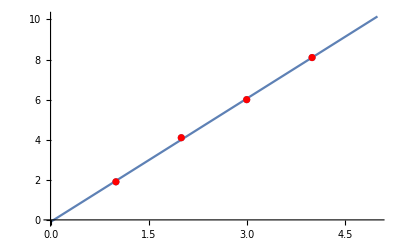

```mathematica
PlotDataAndModel[converter/@data,trained]
```

```mathematica
Clear[net,data, trained];
```

#### Perform logistic regression using neural nets 使用神经网络执行逻辑回归

```mathematica
net=NetChain[{LinearLayer[],LogisticSigmoid}];
data={1->False,2->False,3->True,4->True};
trained=NetTrain[net,data]
```

NetChain[<>]

Make predictions:

作出预测：

```mathematica
trained[{0,1,2,3,4,5},"Probability"]
```

{False,False,False,True,True,True}

Draw a prediction line and plot the data:

画一条预测线并绘制数据：

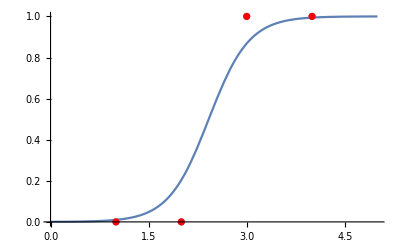

```mathematica
PlotDataAndModel[converter/@data,trained[#,"Probability"]&]
```

```mathematica
Clear[net,data, trained]
```

## NetTrain: Options

## NetTrain：选项

#### LossFunction

The loss layer specifies the functional form of the loss to be computed, e.g. MeanSquaredLossLayer or CrossEntropyLossLayer. We can use  LossFunction -> “loss layer” in NetTrain to specify the loss during training, e.g., 
-损失层指定要计算的损失形式，例如 MeanSquaredLossLayer或CrossEntropyLossLayer。 我们可以在NetTrain中使用LossFunction->“损失层” 来指定训练期间的损失，例如，

```mathematica
trained=NetTrain[net,data,LossFunction->MeanSquaredLossLayer[]]
```

Typical LossLayers are:

典型的 LossLayers 为：

MeanSquaredLossLayer : represents a loss layer that computes the mean squared loss between its “Input” port and “Target” port. (used for regression problems)
代表一个损失层，该损失层计算其“输入”端口和“目标”端口之间的均方损失. （用于回归问题）

```mathematica
data=<|"Input"-> {1,2,3},"Target"->{3,2,1}|>;
MeanSquaredLossLayer[][data]

meanSquaredLoss=N[Mean[Flatten[(#Input-#Target)^2]]]&; 
meanSquaredLoss[data]//N
```

2.66667

2.66667

CrossEntropyLossLayer : computes the cross-entropy loss by comparing  its “Input” port and “Target” port. (used for classification problems)  - 通过比较其“输入”端口和“目标”端口来计算交叉熵损失. （用于分类问题）

```mathematica
data=<|"Input"-> {0.1,0.2,0.7},"Target"->{0.12,0.3,0.6}|>;
CrossEntropyLossLayer["Probabilities"][data]

ceLoss=-Total[#Target*Log@#Input]&;
ceLoss[data]
```

0.973147

0.973147

When a loss layer is chosen automatically for a port, the loss layer to use is based on the layer within the net whose output is connected to the port. For SoftmaxLayer and LogisticSigmoid, CrossEntropyLossLayer is chosen, for LinearLayer layers, MeanSquaredLossLayer is chosen.

当NetTrain为端口自动选择损失层时，要使用的损失层基于其网里连接到端口的层. 对于 SoftmaxLayer 和 LogisticSigmoid，选择CrossEntropyLossLayer，对于LinearLayer，选择 MeanSquaredLossLayer.

#### Method

NetTrain automatically chooses the appropriate Method and LearningRate unless given explicitly.

The available Methods are variations of stochastic gradient descent:

除非明确给出，否则 NetTrain 会自动选择适当的 Method 和 LearningRate.

可用的方法包括各种不同的随机梯度下降：

”ADAM” : stochastic gradient descent using an adaptive learning rate that is invariant to diagonal rescaling of the gradients - “ADAM”：使用自适应学习率的随机梯度下降，该自适应学习率对于梯度的强度没有影响

“RMSProp” : stochastic gradient descent using an adaptive learning rate derived from exponentially smoothed average of gradient magnitude - “RMSProp”：使用自适应学习率的随机梯度下降，该学习率是从梯度幅度的指数平滑平均值中得出的

“SGD”:  ordinary stochastic gradient descent with momentum - “SGD”：具有动量的普通随机梯度下降

Use stochastic gradient descent with momentum to train a simple network: - 使用具有动量的随机梯度下降来训练简单的网络：

```mathematica
data={1->2.2,2->3.8,3->6.4,4->9.1};layer=LinearLayer[];net=NetTrain[layer,data,Method->"SGD"]
```

LinearLayer[<>]

Specify an initial learning rate: - 指定初始学习率：

```mathematica
net=NetTrain[layer,data,Method->{"SGD","LearningRate"->0.1}]
```

LinearLayer[<>]

#### BatchSize

With the default setting of BatchSize->Automatic, batch size is chosen automatically, based on the memory requirements of the network and the memory available on the target device. The maximum batch size that will be automatically chosen is 16.

使用 BatchSize-> Automatic 的默认设置时，将根据网络的内存需求和目标设备上可用的内存自动选择批次大小. 将自动选择的最大批处理大小为 16.

Using a large batch size will typically increase the number of examples that can be evaluated per second as can be seen using MeanInputsPerSecond

使用大批处理量通常会增加每秒可计算的示例数量，如使用 MeanInputsPerSecond 所见

```mathematica
trainingData=RandomReal[1,{10000,4}]->RandomReal[1,{10000,4}];
net=NetChain[{LinearLayer[8],LinearLayer[4]},"Input"->4];
NetTrain[net,trainingData,"MeanInputsPerSecond",BatchSize->512,MaxTrainingRounds->20]
```

388628.

Depending on the task, larger batch sizes provide only a marginal benefit to the final net quality, and may exhaust the available memory when training on a GPU. You may need to reduce the BatchSize for the limitation from GPU memory. Furthermore, training time may be better spent on making more frequent updates using smaller batches, as long as the batch size is still large enough to produce a low-variance estimate.

根据任务的不同，过大的批次大小只会给最终的网络质量带来一点好处，并且在GPU 上进行训练时可能会耗尽可用内存. 您可能需要减小BatchSize 来应对GPU 内存的限制. 此外，只要批次大小足够大以产生低方差估计，训练时间可能会更好地花费在使用较小批次的更频繁更新上.

#### MaxTrainingRounds

MaxTrainingRounds means the number of epoch or how many times to traverse all the training data.

Train a network such that it visits each example exactly once:

MaxTrainingRounds 表示时期数或遍历所有训练数据的次数.

训练一个网络，使其完全访问每个示例一次：

```mathematica
trainingData=RandomReal[1,{10000,4}]->RandomReal[1,{10000,4}];
net=NetChain[{8,4},"Input"->4];
NetTrain[net,trainingData,MaxTrainingRounds->1]
```

NetChain[<>]

Train a network for approximately 5 seconds:

训练网络大约5秒钟：

```mathematica
NetTrain[net,trainingData,MaxTrainingRounds->Quantity[5,"Seconds"]]//AbsoluteTiming
```

{5.13168,NetChain[<>]}

#### TargetDevice

Train a net using the default system GPU, if available:

使用默认系统 GPU 训练网络（如果可用）：

```mathematica
trainingData=RandomReal[1,{10000,4}]->RandomReal[1,{10000,4}];
net=NetChain[{8,4}];
NetTrain[net,trainingData,TargetDevice->"GPU"]
```

NetTrain::trgdevnogpu: TargetDevice -> GPU could not be used; your system does not appear to have a supported NVIDIA GPU.

$Failed

If a compatible GPU is not available, a message is issued and $Failed is returned.

如果没有兼容的 GPU，则会发出一条消息并返回 $ Failed.

```mathematica
Clear["Global`*"]
```

## Classification with Real World Data: Constructing the Network

## 真实数据分类：构建网络

Now we will work with data on survivors of the Titanic to perform logistic regression with both categorical and numerical input data.  The dataset contains information for the passengers travelling in Titanic, the class of travel, their age, their gender and information if they survived or not.

现在，我们将处理泰坦尼克号幸存者的数据，以对分类和数字输入数据执行逻辑回归. 该数据集包含乘坐泰坦尼克号旅行的乘客的信息，旅行类别、他们的年龄、性别以及是否幸存的信息.

Get the data from the Wolfram server, delete incomplete entries, then split the data into training and test datasets.

从 Wolfram 服务器获取数据，删除不完整的条目，然后将数据分为训练和测试数据集.

```mathematica
titanicData=ExampleData[{"Dataset","Titanic"}];
titanicData=DeleteMissing[titanicData,1,2];
{trainingData,testData}=TakeDrop[RandomSample@titanicData,800]
```

{,}

Next we create encoders for the categorical features: class (with 3 values), sex (with 2 values).

接下来，我们为分类特征创建编码器：类（具有3个值），性别（具有2个值）.

```mathematica
classEncoder=NetEncoder[{"Class",{"1st","2nd","3rd"}, "UnitVector"}]
genderEncoder=NetEncoder[{"Class",{"male","female"},"UnitVector"}]
```

NetEncoder[<>]

NetEncoder[<>]

For survived we can use the built-in Boolean decoder.

对于幸存者，我们可以使用内置的布尔值解码器.

We want to combine all the input from the different class encoders, label the input ports, and connect to the first layer.

我们要合并来自不同类编码器的所有输入，标记输入端口，并连接到第一层.

```mathematica
inputNet=NetGraph[{CatenateLayer[]},{{NetPort["class"],NetPort["age"],NetPort["sex"]}->1},"class"-> classEncoder,"age"->"Scalar","sex"-> genderEncoder]
```

NetGraph[<>]

Now we add the layers that perform the logistic regression to the existing inputNet.
Connect the LogisticSigmoid to the appropriate Decoder so that it outputs a Boolean, to indicate if the passenger survived or not.

现在，我们将执行逻辑回归的层添加到现有的 inputNet 中.
将 LogisticSigmoid 连接到适当的解码器，以便输出一个布尔值，来指明乘客是否幸存.

```mathematica
untrainedNet=NetGraph[{inputNet,LinearLayer[],LogisticSigmoid},{1->2->3->NetPort["survived"]},"survived"->"Boolean"]
```

NetGraph[<>]

## Classification with Real World Data: Training, Predicting and Accuracy

## 真实数据分类：训练、预测和准确性

We train the network using NetTrain. The option MaxTrainingRounds specifies how many times the data is revisited. The Training Progress report displays the current iteration and the error function during the training.

我们使用 NetTrain 训练网络. 选项 MaxTrainingRounds 指定重新访问数据的次数. 培训进度报告显示培训期间的当前迭代和错误函数.

```mathematica
trainedNet=NetTrain[untrainedNet,trainingData,MaxTrainingRounds->1000]
```

NetGraph[<>]

Once the network is trained we can enter the input features for fictitious passengers and find the probability for their survival.

一旦对网络进行了训练，我们就可以输入虚拟乘客的输入特征，并找到他们生存的可能性.

```mathematica
trainedNet[<|"class"-> "1st","age"->20,"sex"->"female"|>,#]&/@{"Decision","Probability"}
```

{True,0.949121}

```mathematica
trainedNet[<|"class"-> "3rd","age"->30,"sex"->"male"|>,#]&/@{"Decision","Probability"}
```

{False,0.0774251}

We can take our analysis a step further and plot the probability of survival with age for all the variations in class and gender.

我们可以进一步进行分析，并针对所有类和性别差异绘制随年龄变化的生存概率.

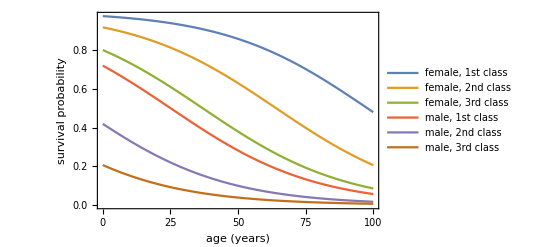

```mathematica
p[class_,age_,sex_]:=trainedNet[<|"class"->class,"age"->age,"sex"->sex|>,"Probability"];
Plot[
{p["1st",x,"female"],p["2nd",x,"female"],p["3rd",x,"female"],
p["1st",x,"male"],p["2nd",x,"male"],p["3rd",x,"male"]},
 {x,0,100},]
```

Assess the accuracy of the network by testing it against the test data set created. Compare the accuracy with the built-in Classify function.

通过针对创建的测试数据集进行测试来评估网络的准确性. 将其准确性与内置的分类功能比较.

ClassifierMeasurements[classifier, testset, prop]: gives measurements associated with property prop when classifier is evaluated on testset. - 在测试集上评估分类器时，给出与属性 prop 相关的度量.

```mathematica
cm=ClassifierMeasurements[trainedNet,testData-> "survived","Accuracy"]
```

0.768293

```mathematica
cf=Classify[trainingData->"survived"];
ClassifierMeasurements[cf,testData->"survived","Accuracy"]
```

0.768293

Save the trained network for future use.

保存经过培训的网络以备将来使用.

```mathematica
Export["titanic.wlnet",trainedNet]
```

titanic.wlnet

## Summary

## 总结

Wolfram Language provides a full framework for building, training and evaluating neural networks.
Wolfram 语言提供了用于构建、训练和評估神经网络的完整框架.

The neural network is a machine learning algorithm with bio-inspired neuron-like structure consisted of various operational layers with learnable parameters. 
神经网络是一种具有生物启发性类神经元结构的机器学习算法，该结构由具有可学习参数的各种操作层组成.

The training process is based on the optimization on loss function, which guides a neural network to update parameters.
训练过程基于损失函数的优化，该函数指导神经网络更新参数.

Roles of layers and functions: - 层和函数的作用：

NetEncoder: converts input data as usable tensor for Neural Networks and and NetDecoder translates output of Neural Networks to target domain. - NetEncoder：将输入数据转换为神经网络的可用张量，而 NetDecoder 将神经网络的输出转换为目标域.

Activation function (a neuron): introduces non-linearity to increase the representational power of the network.
激活函数（神经元）：引入非线性以增加网络的表示能力.

ElementwiseLayer[f]: applies an activation function (AF) f to every element of the input tensor. “ReLU” is the most popular AF.
ElementwiseLayer [f]：将激活函数（AF） f 应用于输入张量的每个元素. “ReLU”是最受欢迎的 AF.

LinearLayer: usually used as fully connected layers in the last layers for rearranging and changing the information dimensions to fit the target domain.
LinearLayer：通常用作最后一层的完全连接层，重整讯息以改变讯息维度配合输出.

ConvolutionLayer : the kernel of any convolutional neural network with learnable filters to extract useful information. 
Filter size and Strides are two important settings.
ConvolutionLayer：卷积神经网络的重要结构，具有可学习的滤波器以提取有用的信息. 
滤波器大小和 Stride 是两个重要设置.

BatchNormalizationLayer: rescale the input based on each batch, for maintaining the training performance and stability.
BatchNormalizationLayer：基于每个批次重整输入，以保持训练效能和稳定性.

DropoutLayer: randomly zero out the channels (neurons) during training; a regularization technique for reducing overfitting in neural networks.
DropoutLayer：在训练过程中将通道（神经元）随机清零；一种减少神经网络过拟合的正则化技术.

PoolingLayer: progressively reduces the spatial size and keep useful information at same time. 
PoolingLayer：逐渐减小讯息在空间维度大小并同时保留有用的信息.

Building the networks: - 构建网络

NetChain : Construct a net consisting different layers in a chain. 
NetChain：构建一个由链中不同层组成的网络.

NetGraph : Construct a graphical neural network of any topology.
NetGraph：构建任何拓扑的图形神经网络.

Network Training ideas : - 网络训练思路：

Loss function: is built as a measure between neural network output and target, and “guides” it to “learn”. 
损失函数：构建神经网络输出和目标之间的度量，并“指导”神经网络“学习”.

Backpropagation: a scheme to update parameters starting from last to the first layer.
反向传播：一种从最后一层到第一层更新参数的方案.

Stochastic Gradient Descent (SGD): each gradient is computed over a batch of training data for computational efficiency and optimization purpose.
随机梯度下降（SGD）：为计算效率和优化目的，在一批训练数据上计算梯度.

Optimization methods: SGD, ADAM, RMSProp are popular optimizers
优化方法：SGD、ADAM、RMSProp 是流行的优化器.

Three important ingredients for Network Training: - 网络训练的三个重要要素：

Network architecture (required input for NetTrain) - 网络体系结构（NetTrain 的必要输入）

Training data (required input for NetTrain) - 训练数据（NetTrain的必要输入）

Loss and optimization methods (options of NetTrain) - 损失和优化方法（NetTrain 的选项）

推薦網頁 :Wolfram 语言中的神经网络综述

## Glossary

## 词汇表

```mathematica
Grid[{{Button[Style["Image classification", "Hyperlink"], 
     NotebookLocate["Image classification"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Optimization", "Hyperlink"], 
     NotebookLocate["optimization"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Gradient Descent", "Hyperlink"], 
     NotebookLocate["Gradient Descent Methods"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["NetEncoder", "Hyperlink"], 
     NotebookLocate["NetEncoder"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Activation function", "Hyperlink"], 
     NotebookLocate["Activation function"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["ElementwiseLayer", "Hyperlink"], 
     NotebookLocate["ElementwiseLayer"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["LinearLayer", "Hyperlink"], 
     NotebookLocate["LinearLayer"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["ConvolutionLayer", "Hyperlink"], 
     NotebookLocate["ConvolutionLayer"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["PoolingLayer", "Hyperlink"], 
     NotebookLocate["PoolingLayer"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["BatchNormalizationLayer", "Hyperlink"], 
     NotebookLocate["BatchNormalizationLayer"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["DropoutLayer", "Hyperlink"], 
     NotebookLocate["DropoutLayer"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["All layers", "Hyperlink"], 
     NotebookLocate["All layers"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["NetChain", "Hyperlink"], 
     NotebookLocate["NetChain"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["NetGraph", "Hyperlink"], 
     NotebookLocate["NetGraph"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Training Theory", "Hyperlink"], 
     NotebookLocate["Training Theory"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["Backpropagation", "Hyperlink"], 
     NotebookLocate["Backpropagation"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Stochastic Gradient Descent", "Hyperlink"], 
     NotebookLocate["Stochastic Gradient Descent"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Epoch", "Hyperlink"], 
     NotebookLocate["epoch"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["NetTrain", "Hyperlink"], 
     NotebookLocate["NetTrain"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Regression Models", "Hyperlink"], 
     NotebookLocate["Regression Models"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["LossFunction(NetTrain)", "Hyperlink"], 
     NotebookLocate["LossFunction"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["Method(NetTrain)", "Hyperlink"], 
     NotebookLocate["Method"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["BatchSize(NetTrain)", "Hyperlink"], 
     NotebookLocate["BatchSize"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["TargetDevice(NetTrain)", "Hyperlink"], 
     NotebookLocate["TargetDevice"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]},{
     Button[Style["ConcenateLayer", "Hyperlink"], 
     NotebookLocate["ConcenateLayer"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["Titanic Data", "Hyperlink"], 
     NotebookLocate["TitanicDataSet"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"],
     Button[Style["ClassifierMeasurements(Accuracy)", "Hyperlink"], 
     NotebookLocate["ClassifierMeasurements"], Appearance -> None, 
     Evaluator -> Automatic, Method -> "Preemptive"]
     }}, Alignment -> Left, 
  Frame -> False, ItemSize -> {Automatic, Automatic}]
```

Image classification | Optimization | Gradient Descent
NetEncoder | Activation function | ElementwiseLayer
LinearLayer | ConvolutionLayer | PoolingLayer
BatchNormalizationLayer | DropoutLayer | All layers
NetChain | NetGraph | Training Theory
Backpropagation | Stochastic Gradient Descent | Epoch
NetTrain | Regression Models | LossFunction(NetTrain)
Method(NetTrain) | BatchSize(NetTrain) | TargetDevice(NetTrain)
ConcenateLayer | Titanic Data | ClassifierMeasurements(Accuracy)

## Initialization code

```mathematica
Iconize[Unevaluated[
converter[x_->y_]:={x,If[BooleanQ[y],If[y,1,0],y]};
PlotDataAndModel[data_,model_]:=Show[Plot[model[x],{x,0,5}],ListPlot[Style[#,Red]&/@data]];
],"Helper functions"]
```